0.98313

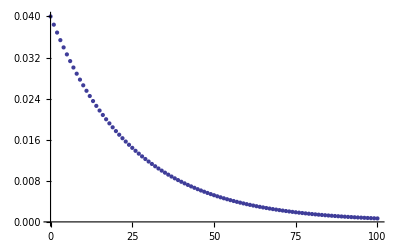

```mathematica
ClearAll[g,p,k];
d=0.04;
m=11+1;
sum=0;
p=0.09;
l=4/d;
gaps=Table[{i,(1-d)^i*d},{i,0,l}];
kaps=Table[{i,(1-d)^i*d},{i,0,l}];
g=gaps[[All,2]];
k=gaps[[All,2]];
For[i=1,i<l+1,i++,
sum+=g[[i]];]
sum
For[i=1,i<l+1,i++,
g[[i]]/=sum;]
data=Table[{i-1,g[[i]]},{i,1,l}];
ListPlot[gaps,PlotRange->Full]
For[j=1,j<500,j++,
For[i=1,i<m,i++,
k[[i]]=0;]
k[[m]]=g[[m-1]]*g[[m-1]]*(1-3*p)+g[[m-1]]*p+g[[m]]*g[[m-1]]*(1-3*p)+g[[m]]*p+g[[m+1]]*g[[m-1]]*p;
k[[m+1]]=-g[[m-1]]*g[[m-1]]*(1-3*p)+g[[m-1]]*(1-2*p)-g[[m]]*g[[m-1]]*(1-3*p)+g[[m]]*(1-2*p)+g[[m+1]]*g[[m-1]]*(1-3*p)+g[[m+1]]*p+g[[m+2]]*g[[m-1]]*p;
k[[m+2]]=-g[[m-1]]*g[[m-1]]*p+g[[m-1]]*p-g[[m]]*g[[m-1]]*p+g[[m]]*p-g[[m+1]]*g[[m-1]]*(1-3*p)+g[[m+1]]*(1-2*p)+g[[m+2]]*g[[m-1]]*(1-3*p)+g[[m+2]]*p+g[[m+3]]*g[[m-1]]*p;
For[i=m+3,i<l-1,i++,
k[[i]]=g[[i-1]]*(-g[[m-1]]*p+p)+g[[i]]*(g[[m-1]]*(3*p-1)+(1-2*p))+g[[i+1]]*(g[[m-1]]*(1-3*p)+p)+g[[i+2]]*g[[m-1]]*p;]
For[i=l-1,i<l+1,i++,
k[[i]]=g[[i]];]
sum=0;
For[i=1,i<l+1,i++,
sum+=k[[i]];]
For[i=1,i<l+1,i++,
g[[i]]=k[[i]]/sum;]



]
```

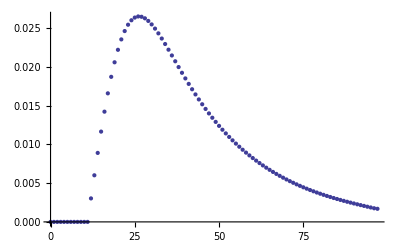

```mathematica
datas=Table[{i-3,g[[i]]},{i,3,l}];
pic=ListPlot[datas,PlotRange->Full];
Show[pic]
```

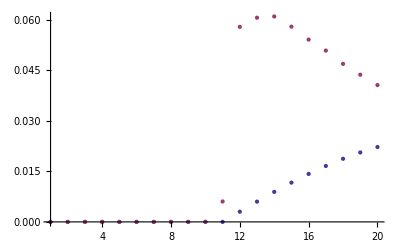

```mathematica
ListPlot[{datas,gapd},PlotRange->{{1,20},Full}]
```

```mathematica
l
```

100.

```mathematica
gaps[[1]]
```

{0,0.02}

```mathematica
k[[1]]
```

0.0203581

```mathematica
g=gaps[[All,2]];
```

```mathematica
g
```

{0.04,0.0384,0.036864,0.0353894,0.0339739,0.0326149,0.0313103,0.0300579,0.0288556,0.0277014,0.0265933,0.0255296,0.0245084,0.0235281,0.0225869,0.0216835,0.0208161,0.0199835,0.0191841,0.0184168,0.0176801,0.0169729,0.016294,0.0156422,0.0150165,0.0144159,0.0138392,0.0132857,0.0127542,0.0122441,0.0117543,0.0112841,0.0108328,0.0103995,0.00998348,0.00958414,0.00920077,0.00883274,0.00847943,0.00814026,0.00781465,0.00750206,0.00720198,0.0069139,0.00663734,0.00637185,0.00611698,0.0058723,0.0056374,0.00541191,0.00519543,0.00498761,0.00478811,0.00459659,0.00441272,0.00423621,0.00406676,0.00390409,0.00374793,0.00359801,0.00345409,0.00331593,0.00318329,0.00305596,0.00293372,0.00281637,0.00270372,0.00259557,0.00249175,0.00239208,0.00229639,0.00220454,0.00211636,0.0020317,0.00195043,0.00187242,0.00179752,0.00172562,0.00165659,0.00159033,0.00152672,0.00146565,0.00140702,0.00135074,0.00129671,0.00124484,0.00119505,0.00114725,0.00110136,0.0010573,0.00101501,0.000974411,0.000935435,0.000898017,0.000862097,0.000827613,0.000794508,0.000762728,0.000732219,0.00070293,0.000674813}

```mathematica
0.02770135983297921/0.028855583159353344
```

0.96